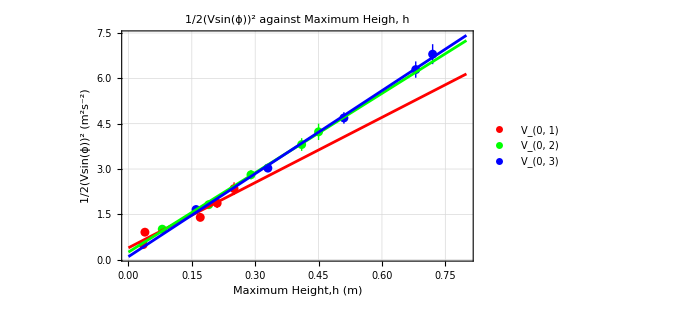
-Graphics-
V_(0, 1): y==7.19187 x+0.393385
V_(0, 2): y==8.75192 x+0.250456
V_(0, 3): y==9.15398 x+0.100088

```mathematica
V1={{0.035,0.50},{0.039,0.91},{0.170,1.40},{0.210,1.87},{0.250,2.35}};
V2={{0.080,1.01},{0.190,1.82},{0.290,2.81},{0.410,3.81},{0.450,4.23}};
V3={{0.160,1.66},{0.330,3.03},{0.510,4.69},{0.680,6.29},{0.720,6.80}};

(*error bar*)
V1error={{Around[0.035,0.001],Around[0.50,0.03]},{Around[0.039,0.001],Around[0.91,0.06]},{Around[0.170,0.001],Around[1.40,0.10]},{Around[0.210,0.001],Around[1.87,0.16]},{Around[0.250,0.001],Around[2.35,0.21]}};

V2error={{Around[0.080,0.001],Around[1.01,0.05]},{Around[0.190,0.001],Around[1.82,0.09]},{Around[0.290,0.001],Around[2.81,0.15]},{Around[0.410,0.001],Around[3.81,0.21]},{Around[0.450,0.001],Around[4.23,0.27]}};

V3error={{Around[0.160,0.001],Around[1.66,0.08]},{Around[0.330,0.001],Around[3.03,0.12]},{Around[0.510,0.001],Around[4.69,0.19]},{Around[0.680,0.001],Around[6.29,0.27]},{Around[0.720,0.001],Around[6.80,0.33]}};

(*Extract x and y values for each set of data*)
x1=V1[[All,1]];
y1=V1[[All,2]];
x2=V2[[All,1]];
y2=V2[[All,2]];
x3=V3[[All,1]];
y3=V3[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V1,x,x];
fit2=LinearModelFit[V2,x,x];
fit3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fit1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fit2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fit3["BestFit"]]];

(*Display the equations outside the graph with extended line plot*)
Column[{Show[ListPlot[{V1error,V2error,V3error},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fit1[x],fit2[x],fit3[x]},{x,0,0.8},PlotStyle->{Red,Green,Blue}],Frame->True,FrameLabel->{"Maximum Height,h (m)","\!\(\*FractionBox[\(1\), \(2\)]\)(Vsin(ϕ)\!\(\*SuperscriptBox[\()\), \(2\)]\) (m^2s^-2)"},GridLines->Automatic,PlotLabel->"\!\(\*FractionBox[\(1\), \(2\)]\)(Vsin(ϕ)\!\(\*SuperscriptBox[\()\), \(2\)]\) against Maximum Heigh, h",ImageSize->500,PlotRange->{{0,0.8},Automatic}],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```